```mathematica
(*working with the eigen energies of the 1D harmonic oscillator*)
```

```mathematica
explicitPartitionfunctionHO[beta_]:=∑_(n=0)^∞ Exp[-beta(n+1/2)]
```

```mathematica
FullSimplify[explicitPartitionfunctionHO[beta]]
```

1/2 Csch[beta/2]

```mathematica
explicitEnergyHO[beta_]:=-D[Log[explicitPartitionfunctionHO[beta]], beta]
```

```mathematica
FullSimplify[explicitEnergyHO[beta]]
```

1/2 Coth[beta/2]

```mathematica
(*these are the 1D harmonic oscillator eigen states*)
```

```mathematica
EigenstatesHO[n_,x_,beta_]:=1/(√(2^n(n!)√π))Exp[-x^2/2]HermiteH[n,x]
```

```mathematica
(*to get the density, we need to square the eigen states and multiply by the wieght factor; of course, we also need to normalize by the partition function*)
```

```mathematica
explicitDensityHO[x_,beta_]:=(∑_(n=0)^∞ (EigenstatesHO[n,x,beta])^2 Exp[-beta(n+1/2)])/FullSimplify[explicitPartitionfunctionHO[beta]]
```

```mathematica
(* we can try to see if Mathemtica can evaluate the infinite sum... turns out that Mathemtica does not know how to do this...*)
```

```mathematica
FullSimplify[explicitDensityHO[x,beta]]
```

2 Sinh[beta/2] ∑_(n=0)^∞ (2^-n ⅇ^(-beta (1/2+n)-x^2) HermiteH[n,x]^2)/(√π n!)

```mathematica
(*if we want to use the explicit expression, we need to change the sum from infinity to a sufficiently large value; here, I am using 100 (if the temperature is really high, then we need to include even more states in the sum)*)
```

```mathematica
explicitDensityCutoffHO[x_,beta_]:=(∑_(n=0)^100 (EigenstatesHO[n,x,beta])^2 Exp[-beta(n+1/2)])/FullSimplify[explicitPartitionfunctionHO[beta]]
```

```mathematica
(*implementing the analytical expressions for the 1D harmonic oscillator from the notes*)
```

```mathematica
densityHO[x_,beta_]:=√(Tanh[beta/2]/π)Exp[-x^2 Tanh[beta/2]]
```

```mathematica
partitionfunctionHO[beta_]:=Exp[-beta/2]/(1-Exp[-beta])
```

```mathematica
energyHO[beta_]:=Coth[beta/2]/2
```

```mathematica
Series[energyHO[beta],{beta,0,2}]
```

1/beta+beta/12+O[beta]^3

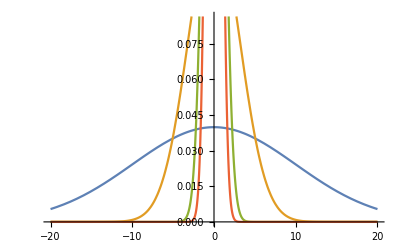

```mathematica
Plot[{densityHO[x,0.01],densityHO[x,0.1],densityHO[x,1],densityHO[x,10]},{x,-20,20}]
```

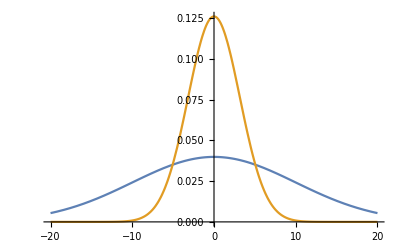

```mathematica
Plot[{densityHO[x,0.01],densityHO[x,0.1]},{x,-20,20}]
```

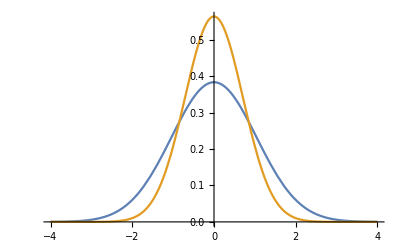

```mathematica
Plot[{densityHO[x,1],densityHO[x,100]},{x,-4,4}]
```

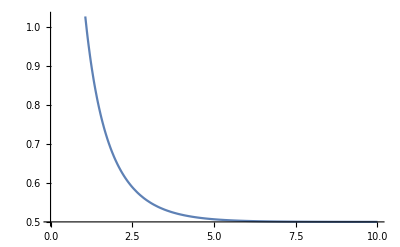

```mathematica
Plot[energyHO[beta],{beta,0,10}]
```

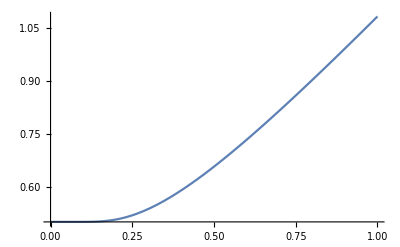

```mathematica
Plot[energyHO[beta]/.beta->1/temp,{temp,0,1}]
```

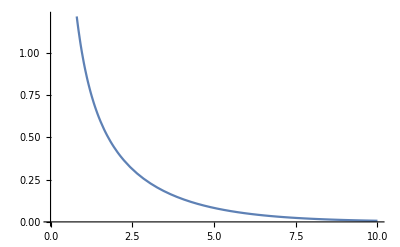

```mathematica
Plot[partitionfunctionHO[beta],{beta,0,10}]
```

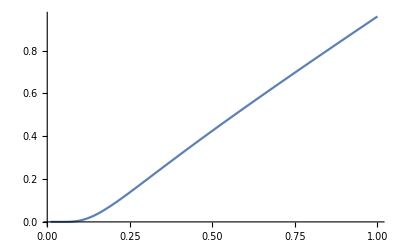

```mathematica
Plot[partitionfunctionHO[beta]/.beta->1/temp,{temp,0.01,1}]
```

```mathematica
(*the following graph compares the analytical expression for the density from class with the "brute-force" implemention above (i.e., the implementation where I introduced a finite cutoff for the sum): as expected, the expressions give the same result!*)
```

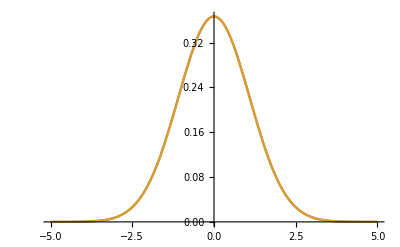

```mathematica
Plot[{explicitDensityCutoffHO[x,0.9],densityHO[x,0.9]},{x,-5,5}]
```